# Red blood cell (axisymmetric) analytical solution

## set up geometry

### z-r parametrization

```mathematica
(*Clear[z]
Clear[r]*)
ClearAll
R = 1;
c0 = 0.2072;
c1 = 2.0026;
c2 = -1.1228;
```

ClearAll

```mathematica
ClearAll::usage
```

ClearAll[symb_1,symb_2,…] clears all values, definitions, attributes, messages, and defaults associated with symbols. 
ClearAll[form,form,…] clears all symbols whose names textually match any of the form_i.

```mathematica
z = .5 * R * √(1-(r/R)^2)(c0 + c1 * (r/R)^2 + c2 * (r/R)^4)
(*z = 2 √(1 - r^2)*)
```

0.5 √(1-r^2) (0.2072+2.0026 r^2-1.1228 r^4)

```mathematica
z[0.6]
```

0.313048/;0<0.6<R

```mathematica
N[inv[0.313]]
```

z^(-1)[0.313]

```mathematica
N[Integrate[inv,{z,0,  N[z[0.8 *R]]}]]
```

NIntegrate::nlim: z = 0.30869/;0.<0.8<R is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

NIntegrate[z^(-1),{z,0,0.30869/;0.<0.8<R}]

NIntegrate[z^(-1),{z,0,0.30869/;0<0.8<R}]

∫_0^(0.30869/;0<0.8<R) z^(-1)ⅆz

z^(-1)[0.1]

z^(-1)[0.2]

### plotting

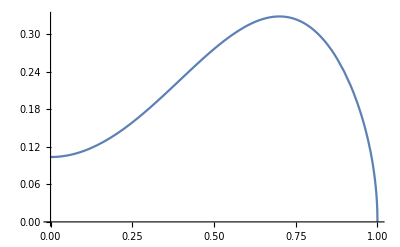

```mathematica
Plot[z,{r, 0, 1}]
(*PlotPure[fun_,d_,args___]:=Plot[Evaluate@If[ListQ[fun],Through[fun[x]],fun[x]],{x,d[[1]],d[[2]]},args];*)
(*PlotPure[z,{0,1}]*)
```

### Differentiation

```mathematica
zPrime= D[z,r];
zPrimePrime = D[z, {r, 2}];
drds = (1 + zPrime^2)^(-0.5);
dsdr = (1 + zPrime^2)^(0.5);
```

### arc length

```mathematica
arcLength =Integrate[dsdr,{r,0,R}]
```

### curvature

```mathematica
(*kappaNu = drds * zPrime / r;*)
(*kappaT = drds^3 * zPrimePrime;*)
kappaNu = zPrime/ (r * √(1+zPrime^2))
kappaT = zPrimePrime / (1+ zPrime^2)^1.5
meanCurvature = -0.5 * (kappaNu + kappaT);
gaussianCurvature = kappaNu * kappaT;
```

-2/(√(1-r^2) √(1+(4 r^2)/(1-r^2)))

(2 (-r^2/((1-r^2)^(3/2))-1/(√(1-r^2))))/((1+(4 r^2)/(1-r^2))^1.5)

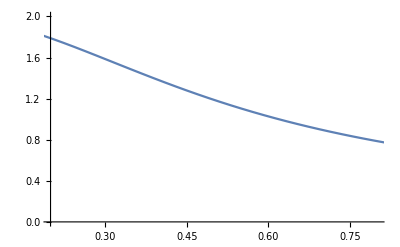

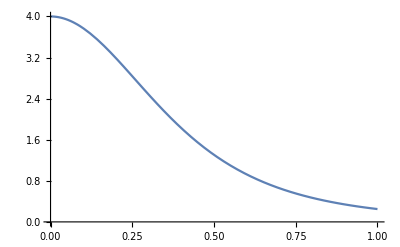

```mathematica
Plot[meanCurvature,{r,0,R}, PlotRange->{{0.2, 0.8},{0,2}}]
Plot[gaussianCurvature,{r,0,R}]
```

```mathematica
totalMeanCurvature = 2 * N[Integrate[meanCurvature* 2 * Pi * r * dsdr ,{r,0,0.99}]]
(*totalMeanCurvatureSquared = 2 * N[Integrate[meanCurvature^2* 2 * Pi * r * dsdr ,{r,0,R}]]
volume = 2 * N[Integrate[1/3 * (z - r * zPrime) * 2 * Pi * r, {r, 0, R}]]*)
(*surfaceArea = 2 * N[Integrate[2 * Pi * r* dsdr, {2, 0, R}]]*)
(*totalGaussianCurvature = 2 * N[Integrate[gaussianCurvature* 2 * Pi * r * dsdr ,{r,0,R}]]*)
```

$Aborted

```mathematica
laplacianH = D[D[meanCurvature,r]* drds, r] * drds / r
Plot[z,{r, 0.5, 0.3}]
(*Plot[laplacianH + 2 * meanCurvature * (meanCurvature^2-gaussianCurvature), {r, 0, R}]*)
```

(-((0.5 ((15. (0.5 (4.0052-13.4736 r^2) √(1-r^2)-(1. r (4.0052 r-4.4912 r^3))/(√(1-r^2))-(0.5 r^2 (0.2072+2.0026 r^2-1.1228 r^4))/((1-r^2)^(3/2))-(0.5 (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2)))^2 (0.5 √(1-r^2) (4.0052 r-4.4912 r^3)-(0.5 r (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2)))^2 (0.5 (4.0052-13.4736 r^2) √(1-r^2)-(1. r (4.0052 r-4.4912 r^3))/(√(1-r^2))+0.5 (0.2072+2.0026 r^2-1.1228 r^4) (-r^2/((1-r^2)^(3/2))-1/(√(1-r^2)))))/(1+(0.5 √(1-r^2) (4.0052 r-4.4912 r^3)-(0.5 r (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2)))^2)^3.5+(3. (0.5 (4.0052-13.4736 r^2) √(1-r^2)-(1. r (4.0052 r-4.4912 r^3))/(√(1-r^2))-(0.5 r^2 (0.2072+2.0026 r^2-1.1228 r^4))/((1-r^2)^(3/2))-(0.5 (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2)))^2 (0.5 √(1-r^2) (4.0052 r-4.4912 r^3)-(0.5 r (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2)))^3)/(r (1+(0.5 √(1-r^2) (4.0052 r-4.4912 r^3)-(0.5 r (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2)))^2)^2.5)-(6. (0.5 (4.0052-13.4736 r^2) √(1-r^2)-(1. r (4.0052 r-4.4912 r^3))/(√(1-r^2))-(0.5 r^2 (0.2072+2.0026 r^2-1.1228 r^4))/((1-r^2)^(3/2))-(0.5 (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2))) (0.5 √(1-r^2) (4.0052 r-4.4912 r^3)-(0.5 r (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2))) (-(1.5 r (4.0052-13.4736 r^2))/(√(1-r^2))-13.4736 r √(1-r^2)-(1. r^2 (4.0052 r-4.4912 r^3))/((1-r^2)^(3/2))-(1. (4.0052 r-4.4912 r^3))/(√(1-r^2))+0.5 (0.2072+2.0026 r^2-1.1228 r^4) (-(3 r^3)/((1-r^2)^(5/2))-(3 r)/((1-r^2)^(3/2)))+0.5 (4.0052 r-4.4912 r^3) (-r^2/((1-r^2)^(3/2))-1/(√(1-r^2)))))/(1+(0.5 √(1-r^2) (4.0052 r-4.4912 r^3)-(0.5 r (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2)))^2)^2.5-(3. (0.5 (4.0052-13.4736 r^2) √(1-r^2)-(1. r (4.0052 r-4.4912 r^3))/(√(1-r^2))-(0.5 r^2 (0.2072+2.0026 r^2-1.1228 r^4))/((1-r^2)^(3/2))-(0.5 (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2)))^2 (0.5 (4.0052-13.4736 r^2) √(1-r^2)-(1. r (4.0052 r-4.4912 r^3))/(√(1-r^2))+0.5 (0.2072+2.0026 r^2-1.1228 r^4) (-r^2/((1-r^2)^(3/2))-1/(√(1-r^2)))))/(1+(0.5 √(1-r^2) (4.0052 r-4.4912 r^3)-(0.5 r (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2)))^2)^2.5-(3. (-(1.5 r (4.0052-13.4736 r^2))/(√(1-r^2))-13.4736 r √(1-r^2)-(1.5 r^2 (4.0052 r-4.4912 r^3))/((1-r^2)^(3/2))-(1.5 (4.0052 r-4.4912 r^3))/(√(1-r^2))-(1.5 r^3 (0.2072+2.0026 r^2-1.1228 r^4))/((1-r^2)^(5/2))-(1.5 r (0.2072+2.0026 r^2-1.1228 r^4))/((1-r^2)^(3/2))) (0.5 √(1-r^2) (4.0052 r-4.4912 r^3)-(0.5 r (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2))) (0.5 (4.0052-13.4736 r^2) √(1-r^2)-(1. r (4.0052 r-4.4912 r^3))/(√(1-r^2))+0.5 (0.2072+2.0026 r^2-1.1228 r^4) (-r^2/((1-r^2)^(3/2))-1/(√(1-r^2)))))/(1+(0.5 √(1-r^2) (4.0052 r-4.4912 r^3)-(0.5 r (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2)))^2)^2.5-(3. (0.5 (4.0052-13.4736 r^2) √(1-r^2)-(1. r (4.0052 r-4.4912 r^3))/(√(1-r^2))-(0.5 r^2 (0.2072+2.0026 r^2-1.1228 r^4))/((1-r^2)^(3/2))-(0.5 (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2)))^2 (0.5 √(1-r^2) (4.0052 r-4.4912 r^3)-(0.5 r (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2))))/(r (1+(0.5 √(1-r^2) (4.0052 r-4.4912 r^3)-(0.5 r (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2)))^2)^1.5)-(1. (-(1.5 r (4.0052-13.4736 r^2))/(√(1-r^2))-13.4736 r √(1-r^2)-(1.5 r^2 (4.0052 r-4.4912 r^3))/((1-r^2)^(3/2))-(1.5 (4.0052 r-4.4912 r^3))/(√(1-r^2))-(1.5 r^3 (0.2072+2.0026 r^2-1.1228 r^4))/((1-r^2)^(5/2))-(1.5 r (0.2072+2.0026 r^2-1.1228 r^4))/((1-r^2)^(3/2))) (0.5 √(1-r^2) (4.0052 r-4.4912 r^3)-(0.5 r (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2)))^2)/(r (1+(0.5 √(1-r^2) (4.0052 r-4.4912 r^3)-(0.5 r (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2)))^2)^1.5)+(2. (0.5 (4.0052-13.4736 r^2) √(1-r^2)-(1. r (4.0052 r-4.4912 r^3))/(√(1-r^2))-(0.5 r^2 (0.2072+2.0026 r^2-1.1228 r^4))/((1-r^2)^(3/2))-(0.5 (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2))) (0.5 √(1-r^2) (4.0052 r-4.4912 r^3)-(0.5 r (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2)))^2)/(r^2 (1+(0.5 √(1-r^2) (4.0052 r-4.4912 r^3)-(0.5 r (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2)))^2)^1.5)+(-(2.5 r^2 (4.0052-13.4736 r^2))/((1-r^2)^(3/2))+(53.8944 r^2)/(√(1-r^2))-(2.5 (4.0052-13.4736 r^2))/(√(1-r^2))-13.4736 √(1-r^2)-(3. r^3 (4.0052 r-4.4912 r^3))/((1-r^2)^(5/2))-(3. r (4.0052 r-4.4912 r^3))/((1-r^2)^(3/2))+0.5 (0.2072+2.0026 r^2-1.1228 r^4) (-(15 r^4)/((1-r^2)^(7/2))-(18 r^2)/((1-r^2)^(5/2))-3/((1-r^2)^(3/2)))+1. (4.0052 r-4.4912 r^3) (-(3 r^3)/((1-r^2)^(5/2))-(3 r)/((1-r^2)^(3/2)))+0.5 (4.0052-13.4736 r^2) (-r^2/((1-r^2)^(3/2))-1/(√(1-r^2))))/(1+(0.5 √(1-r^2) (4.0052 r-4.4912 r^3)-(0.5 r (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2)))^2)^1.5+(-(1.5 r (4.0052-13.4736 r^2))/(√(1-r^2))-13.4736 r √(1-r^2)-(1.5 r^2 (4.0052 r-4.4912 r^3))/((1-r^2)^(3/2))-(1.5 (4.0052 r-4.4912 r^3))/(√(1-r^2))-(1.5 r^3 (0.2072+2.0026 r^2-1.1228 r^4))/((1-r^2)^(5/2))-(1.5 r (0.2072+2.0026 r^2-1.1228 r^4))/((1-r^2)^(3/2)))/(r (1+(0.5 √(1-r^2) (4.0052 r-4.4912 r^3)-(0.5 r (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2)))^2)^0.5)-(2 (0.5 (4.0052-13.4736 r^2) √(1-r^2)-(1. r (4.0052 r-4.4912 r^3))/(√(1-r^2))-(0.5 r^2 (0.2072+2.0026 r^2-1.1228 r^4))/((1-r^2)^(3/2))-(0.5 (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2))))/(r^2 (1+(0.5 √(1-r^2) (4.0052 r-4.4912 r^3)-(0.5 r (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2)))^2)^0.5)+(2 (0.5 √(1-r^2) (4.0052 r-4.4912 r^3)-(0.5 r (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2))))/(r^3 (1+(0.5 √(1-r^2) (4.0052 r-4.4912 r^3)-(0.5 r (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2)))^2)^0.5)))/(1+(0.5 √(1-r^2) (4.0052 r-4.4912 r^3)-(0.5 r (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2)))^2)^0.5)+(0.5 (0.5 (4.0052-13.4736 r^2) √(1-r^2)-(1. r (4.0052 r-4.4912 r^3))/(√(1-r^2))-(0.5 r^2 (0.2072+2.0026 r^2-1.1228 r^4))/((1-r^2)^(3/2))-(0.5 (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2))) (0.5 √(1-r^2) (4.0052 r-4.4912 r^3)-(0.5 r (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2))) (-((3. (0.5 (4.0052-13.4736 r^2) √(1-r^2)-(1. r (4.0052 r-4.4912 r^3))/(√(1-r^2))-(0.5 r^2 (0.2072+2.0026 r^2-1.1228 r^4))/((1-r^2)^(3/2))-(0.5 (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2))) (0.5 √(1-r^2) (4.0052 r-4.4912 r^3)-(0.5 r (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2))) (0.5 (4.0052-13.4736 r^2) √(1-r^2)-(1. r (4.0052 r-4.4912 r^3))/(√(1-r^2))+0.5 (0.2072+2.0026 r^2-1.1228 r^4) (-r^2/((1-r^2)^(3/2))-1/(√(1-r^2)))))/(1+(0.5 √(1-r^2) (4.0052 r-4.4912 r^3)-(0.5 r (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2)))^2)^2.5)-(1. (0.5 (4.0052-13.4736 r^2) √(1-r^2)-(1. r (4.0052 r-4.4912 r^3))/(√(1-r^2))-(0.5 r^2 (0.2072+2.0026 r^2-1.1228 r^4))/((1-r^2)^(3/2))-(0.5 (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2))) (0.5 √(1-r^2) (4.0052 r-4.4912 r^3)-(0.5 r (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2)))^2)/(r (1+(0.5 √(1-r^2) (4.0052 r-4.4912 r^3)-(0.5 r (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2)))^2)^1.5)+(-(1.5 r (4.0052-13.4736 r^2))/(√(1-r^2))-13.4736 r √(1-r^2)-(1. r^2 (4.0052 r-4.4912 r^3))/((1-r^2)^(3/2))-(1. (4.0052 r-4.4912 r^3))/(√(1-r^2))+0.5 (0.2072+2.0026 r^2-1.1228 r^4) (-(3 r^3)/((1-r^2)^(5/2))-(3 r)/((1-r^2)^(3/2)))+0.5 (4.0052 r-4.4912 r^3) (-r^2/((1-r^2)^(3/2))-1/(√(1-r^2))))/(1+(0.5 √(1-r^2) (4.0052 r-4.4912 r^3)-(0.5 r (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2)))^2)^1.5+(0.5 (4.0052-13.4736 r^2) √(1-r^2)-(1. r (4.0052 r-4.4912 r^3))/(√(1-r^2))-(0.5 r^2 (0.2072+2.0026 r^2-1.1228 r^4))/((1-r^2)^(3/2))-(0.5 (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2)))/(r (1+(0.5 √(1-r^2) (4.0052 r-4.4912 r^3)-(0.5 r (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2)))^2)^0.5)-(0.5 √(1-r^2) (4.0052 r-4.4912 r^3)-(0.5 r (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2)))/(r^2 (1+(0.5 √(1-r^2) (4.0052 r-4.4912 r^3)-(0.5 r (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2)))^2)^0.5)))/(1+(0.5 √(1-r^2) (4.0052 r-4.4912 r^3)-(0.5 r (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2)))^2)^1.5)/(r (1+(0.5 √(1-r^2) (4.0052 r-4.4912 r^3)-(0.5 r (0.2072+2.0026 r^2-1.1228 r^4))/(√(1-r^2)))^2)^0.5)

-Graphics-